```mathematica
r12 := (r2 - a2  Exp[I ϕ2])/(1-r2   a2  Exp[I ϕ2])
trans:=(r1 - r12 a1  Exp[I ϕ1])/(1-r1  r12  a1  Exp[I ϕ1])
```

```mathematica
n:=3.45;
c := 299792458;
R1:=10 10^(-6);
R2:=10 10^(-6);
d1:= 2 Pi R1
d2:= 2 Pi R2
λ:=1550 10^(-9); (* resonant wavelength *)
Q1:=1×10^5;
Q2:=1×10^6;
g1 := 10.99
g2 := 0.00
α1:=(2 Pi n)/(λ  Q1)
α2:=(2 Pi n)/(λ  Q2)
a1:= Exp[g1- α1 d1]
a2:= Exp[g2- α2 d2]
t1:=√(1-r1^2)
t2:=√(1-r2^2)
t3:=√(1-r3^2)
r1:= 0.68999999
r2:= 0.99989999
```

```mathematica
ϕ2 := ϕ1
```

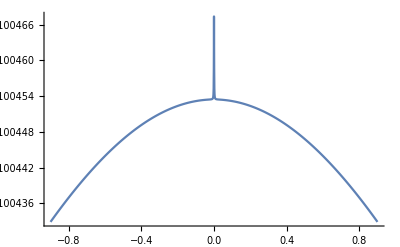

```mathematica
ϕ1min:=-0.9;
ϕ1max:=0.9;
transdata:=Table[{ϕ1,Abs[trans]^2},{ϕ1,ϕ1min, ϕ1max, 0.001}]
ListLinePlot[transdata,PlotRange->All]
```

```mathematica
ϕ12 :=   -ArcTan[(a2  Sin[ϕ1])/(r2-a2 Cos[ϕ1])] + ArcTan[(r2 a2  Sin[ϕ1])/(1- r2 a2 Cos[ϕ1])]
ϕeff := -ArcTan[(a1 Abs[r12] Sin[ϕ1 + ϕ12])/(r1-a1 Abs[r12] Cos[ϕ1 + ϕ12])] + ArcTan[(r1 a1 Abs[r12] Sin[ϕ1 + ϕ12])/(1- r1 a1 Abs[r12] Cos[ϕ1 + ϕ12])]
vg := (n/c) ((a1 (-1+r1^2) Abs[r12] (-a1 (1+r1^2) Abs[r12]+r1 Cos[ϕ1+ϕ12]+a1^2 r1 Abs[r12]^2 Cos[ϕ1+ϕ12]))/((r1^2+a1^2 Abs[r12]^2-2 a1 r1 Abs[r12] Cos[ϕ1+ϕ12]) (1+a1^2 r1^2 Abs[r12]^2-2 a1 r1 Abs[r12] Cos[ϕ1+ϕ12])))
```

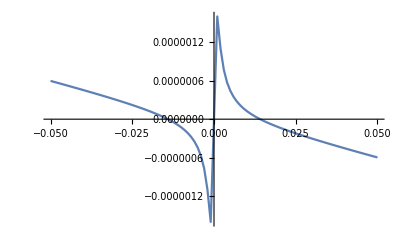

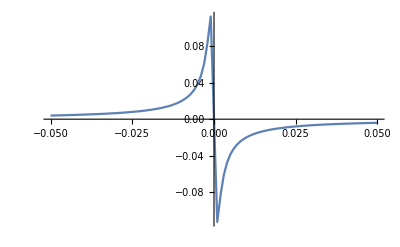

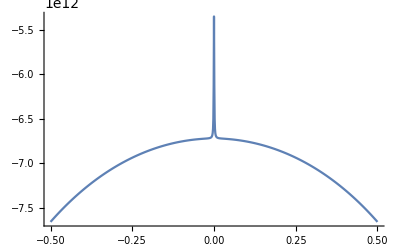

```mathematica
ϕ1min:=-0.05;
ϕ1max:=0.05;
transdata:=Table[{ϕ1,ϕeff},{ϕ1,ϕ1min, ϕ1max, 0.001}]
ListLinePlot[transdata,PlotRange->All]
transdata:=Table[{ϕ1,ϕ12},{ϕ1,ϕ1min, ϕ1max, 0.001}]
ListLinePlot[transdata,PlotRange->All]
transdata:=Table[{ϕ1,1/vg},{ϕ1,-0.5, 0.5, 0.001}]
ListLinePlot[transdata,PlotRange->All]
```

```mathematica
r1 - Abs(r12)a1 /. ϕ1->0
r1 - r2 a1 
r2 - a2
```

0.9989+0.50004 Abs

-3.43869

-0.000222683

```mathematica
(1/vg) /. ϕ1->0
```

-5.3502×10^12